Funciones puras anónimas

Después de los ejemplos que se han visto en Wolfram Language, se puede pasar a un nivel de abstracción ligeramente más elevado, y abordar el concepto, muy importante, de las funciones puras (también llamadas funciones puras anónimas).

El uso de las funciones puras dará paso a un nuevo nivel de capacidades en Wolfram Language, y permitirá reformular algunas de las cosas que ya se han hecho de manera más simple y elegante.

Para empezar, se toma un ejemplo sencillo. Dada una lista de imágenes, se quiere aplicar Blur a cada una. Esto se logra fácilmente mediante /@.

Aplique Blur a cada una de las imágenes en la lista:

```mathematica
Blur/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

Ahora, supóngase que se quiere incluir el parámetro 5 en Blur. ¿Cómo hacerlo? La respuesta es usar una función pura.

Incluya un parámetro mediante la introducción de una función pura:

```mathematica
Blur[#,5]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

La borrosidad original, escrita en términos de una función pura:

```mathematica
Blur[#]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

El # es una “ranura” donde se coloca cada elemento. El & indica que lo que está escrito antes de él es una función pura.

Aquí se presenta en detalle el equivalente de Blur[#,5]&/@... :

```mathematica
{Blur[-Graphics-,5],Blur[-Graphics-,5],Blur[-Graphics-,5]}
```

{-Graphics-,-Graphics-,-Graphics-}

Se verán a continuación otros ejemplos. En cada ocasión, la ranura indica dónde ha de colocarse cada elemento al aplicar la función pura.

Aplique una rotación de 90° a cada cadena de caracteres:

```mathematica
Rotate[#,90Degree]&/@{"one","two","three"}
```

{one,two,three}

Tome una cadena de caracteres y hágala girar en diferentes ángulos:

```mathematica
Rotate["hello",#]&/@{30°,90°,180°,220°}
```

{hello,hello,hello,hello}

Muestre texto en una lista de colores diferentes:

```mathematica
Style["hello",20,#]&/@{Red,Orange,Blue,Purple}
```

{hello,hello,hello,hello}

Cree círculos de diferentes tamaños:

```mathematica
Graphics[Circle[ ],ImageSize->#]&/@{20,40,30,50,10}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Muestre colores y sus negativos en columnas enmarcadas:

```mathematica
Framed[Column[{#,ColorNegate[#]}]]&/@{Red,Green,Blue,Purple,Orange}
```

{RGBColor[1, 0, 0]
RGBColor[0., 1., 1.],RGBColor[0, 1, 0]
RGBColor[1., 0., 1.],RGBColor[0, 0, 1]
RGBColor[1., 1., 0.],RGBColor[0.5, 0, 0.5]
RGBColor[0.5, 1., 0.5],RGBColor[1, 0.5, 0]
RGBColor[0., 0.5, 1.]}

Calcule las longitudes de tres artículos de Wikipedia:

```mathematica
StringLength[WikipediaData[#]]&/@{"apple","peach","pear"}
```

{31045,24153,11115}

Empareje los temas con sus resultados:

```mathematica
{#,StringLength[WikipediaData[#]]}&/@{"apple","peach","pear"}
```

{{apple,31045},{peach,24153},{pear,11115}}

Haga una rejilla con todo ello:

```mathematica
Grid[{#,StringLength[WikipediaData[#]]}&/@{"apple","peach","pear"}]
```

apple | 31045
peach | 24153
pear | 11115

Lo siguiente forma una lista de dígitos y mapea una función pura sobre ella:

```mathematica
Style[#,Hue[#/10],5*#]&/@IntegerDigits[2^100]
```

{1,2,6,7,6,5,0,6,0,0,2,2,8,2,2,9,4,0,1,4,9,6,7,0,3,2,0,5,3,7,6}

Esto es lo que la función pura haría al mapearse sobre {6,8,9}:

```mathematica
{Style[6,Hue[6/10],5*6],Style[8,Hue[8/10],5*8],Style[9,Hue[9/10],5*9]}
```

{6,8,9}

Vistos los anteriores ejemplos de las funciones puras en acción, se revisará, de manera más abstracta, lo que sucede.

Lo siguiente mapea una función pura abstracta sobre una lista:

```mathematica
f[#,x]&/@{a,b,c,d,e}
```

{f[a,x],f[b,x],f[c,x],f[d,x],f[e,x]}

A continuación, el ejemplo mínimo:

```mathematica
f[#]&/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

Eso es equivalente a:

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

Las ranuras se pueden colocar en cualquier parte de la función pura y tantas veces como se quiera. Todas ellas se llenarán con aquello a lo que se esté aplicando la función pura.

Se aplica ahora una función pura ligeramente más complicada:

```mathematica
f[#,{x,#},{#,#}]&/@{a,b,c}
```

{f[a,{x,a},{a,a}],f[b,{x,b},{b,b}],f[c,{x,c},{c,c}]}

Lo anterior se lee con mayor facilidad si se coloca en una columna:

```mathematica
f[#,{x,#},{#,#}]&/@{a,b,c}//Column
```

f[a,{x,a},{a,a}]
f[b,{x,b},{b,b}]
f[c,{x,c},{c,c}]

Ahora se puede analizar ya cómo trabajan, en realidad, las funciones puras. Al escribir f[x], se está aplicando la función f a x. Muchas veces se usa alguna función con un nombre específico en vez de f, por ejemplo, Blur, de modo que se tiene Blur[x], etc.

El asunto es que se puede también reemplazar la f con una función pura. Entonces, la ranura que aparece en la función pura se llenará con el argumento al que se quiere aplicar.

Al aplicar una función pura a x, la ranura # se llena con x:

```mathematica
f[#,a]&  [x]
```

f[x,a]

Una forma equivalente, escrita con @ en vez de [ ... ]:

```mathematica
f[#,a]& @ x
```

f[x,a]

Ahora se puede ver lo que hace /@: simplemente aplica la función pura a cada elemento de la lista.

```mathematica
f[#,a]&/@{x,y,z}
```

{f[x,a],f[y,a],f[z,a]}

Lo mismo, pero escrito de manera más explícita:

```mathematica
{f[#,a]& @ x, f[#,a]& @ y, f[#,a]& @ z}
```

{f[x,a],f[y,a],f[z,a]}

¿Por qué es útil esto? Primero, porque es el fundamento de todo lo que las funciones puras hacen con /@. Pero, de hecho, a menudo es útil por sí mismo; por ejemplo, es una forma de evitar repeticiones.

Aquí está un ejemplo de una función pura donde aparece tres veces la #.

Aplique una función pura a Blend[{Red,Yellow}]:

```mathematica
Column[{#,ColorNegate[#],#}]& [Blend[{Red,Yellow}]]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

Si no se usara la función pura, habría que ponerlo como sigue:

```mathematica
Column[{Blend[{Red,Yellow}],ColorNegate[Blend[{Red,Yellow}]],Blend[{Red,Yellow}]}]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

En Wolfram Language, una función pura trabaja de la misma forma que cualquier otra cosa. Sin embargo, por sí sola, no hace nada.

Si se introduce una función pura por sí sola, regresará sin cambios:

```mathematica
f[#,2]&
```

f[#1,2]&

Sin embargo, si se escribe con la función Map (/@) llevará a cabo un cálculo.

Map usa la función pura para efectuar un cálculo:

```mathematica
Map[f[#,2]&,{a,b,c,d,e}]
```

{f[a,2],f[b,2],f[c,2],f[d,2],f[e,2]}

Se verán cada vez más usos de las funciones puras a lo largo de las próximas secciones.

Vocabulario

código& |   | una función pura 
# |   | ranura en una función pura

"8 Exercises Available"
"with 1 extras" | "Get Started »"

Use Range y una función pura para crear una lista de los 20 primeros cuadrados. »

| Expected output: |  
  | {1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400} |

Forme una lista con los resultados de mezclar el amarillo, el verde y el azul con el rojo. »

| Expected output: |  
  | {RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]} |

Genere una lista de columnas enmarcadas que contengan las versiones mayúscula y minúscula de cada letra del alfabeto inglés. »

| Expected output: |  
  | {"A"
"a","B"
"b","C"
"c","D"
"d","E"
"e","F"
"f","G"
"g","H"
"h","I"
"i","J"
"j","K"
"k","L"
"l","M"
"m","N"
"n","O"
"o","P"
"p","Q"
"q","R"
"r","S"
"s","T"
"t","U"
"u","V"
"v","W"
"w","X"
"x","Y"
"y","Z"
"z"} |

Forme una lista de las letras del alfabeto inglés en colores aleatorios y enmarcadas con colores de trasfondo aleatorios. »

| Sample expected output: |  
  | {"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"} |

Genere una lista de los países del G5 y sus banderas, acomodando el resultado en una rejilla totalmente enmarcada. »






| Expected output: |  
  | "France" | -Graphics-
"Germany" | -Graphics-
"Japan" | -Graphics-
"United Kingdom" | -Graphics-
"United States" | -Graphics- |

Construya una lista con las nubes de palabras de los artículos en Wikipedia sobre “apple”, “peach” y “pear”. »

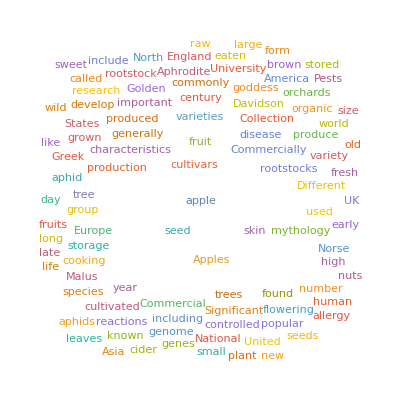
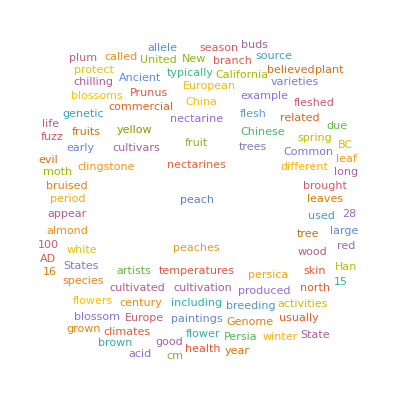
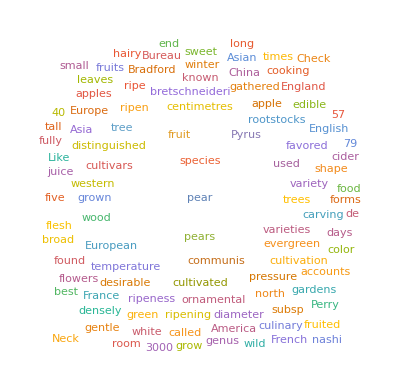
| Sample expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Forme la lista de los histogramas de las longitudes de palabra de los artículos en Wikipedia sobre “apple”, “peach” y “pear”. »

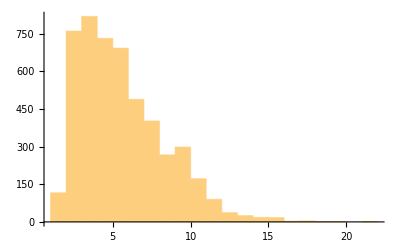
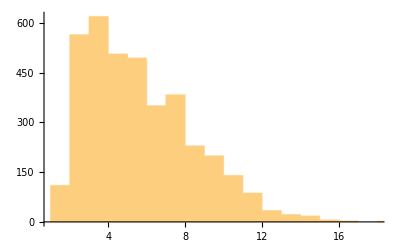
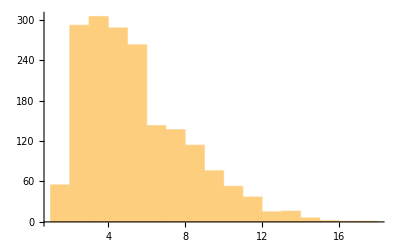
| Sample expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Haga una lista de los mapas de Centroamérica, con cada país resaltado, caso por caso. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Escriba de una manera más simple (#^2+1&)/@Range[10]. »

| Expected output: |  
  | {2,5,10,17,26,37,50,65,82,101} |

Preguntas y respuestas

¿Por qué se les llama “funciones puras”?

Porque lo único que hacen es servir como funciones que se aplican a argumentos. También se les llama funciones anónimas porque, a diferencia de Blur, por ejemplo, no tienen un nombre. Se usan aquí ambos términos, como en “funciones puras anónimas”, para dar a entender los dos significados.

¿Por qué se necesita el &?

El & (ampersand) indica que lo que viene antes de él es el “cuerpo” de una función pura y no el nombre de una función. f/@{1,2,3} da {f[1],f[2],f[3]}, pero f&/@{1,2,3} da {f,f,f}.

¿Cómo se interpreta f[#,1]& ?

Function[f[#,1]]. En este caso Function se llama a veces la “función función”.

Notas técnicas

Las funciones puras son características de la programación funcional. Se suelen llamar expresiones lambda, nombre derivado de su utilización en la lógica matemática en los años 1930s. Se presta a confusión el hecho de que el término “función pura” a veces se refiera a una función que no tiene efectos colaterales (esto es, que no asigne valores a variables, etc.)

Table[f[x],{x,{a,b,c}}] efectivamente hace lo mismo que f/@{a,b,c}. A veces es útil, en especial cuando no se quiere entrar a explicar lo que son las funciones puras.

¡Debe tener cuidado cuando se tienen varios & anidados en una expresión! A veces será necesario insertar paréntesis. Y, a veces, habrá de usarse Function con una variable denominada, como en Function[x,x^2] más que #^2&, para evitar conflictos entre posibles usos de # para funciones diferentes.

En ocasiones se puede obtener código más presentable si se escribe Function[x,x^2] como x↦x^2. La ↦ puede escribirse como \ [Function] o escfnesc. La forma del tipo x ↦x^2 coincide con la notación matemática estándar para “x se mapea a x^2” o “x se convierte en x^2”.

Frecuentemente las opciones pueden ser funciones puras. Es importante encerrar la función pura completa entre paréntesis, como en ColorFunction→(Hue[#/4]&), para evitar una interpretación no deseada.

Para explorar más

Guía para la programación funcional en Wolfram Language »